```mathematica
Clear["Global`*"]
```

```mathematica
(* Functions to form Butcher matrices/vectors given coefficients. S# stands for #-order SDIRK, where the diagonal entry is given first in the parameters, and D# stands for #-order DIRK. *)
S1[ad_]:={{ad}};
S2[ad_,a21_] :={{ad,0},{a21,ad}};
D2[a11_,a21_,a22_] :={{a11,0},{a21,a22}};
S3[ad_,a21_,a31_,a32_] :={{ad,0,0},{a21,ad,0},{a31,a32,ad}};
D3[a11_,a21_,a22_,a31_,a32_,a33_] :={{a11,0,0},{a21,a22,0},{a31,a32,a33}};
S4[ad_,a21_,a31_,a32_,a41_,a42_,a43_] :={{ad,0,0,0},{a21,ad,0,0},{a31,a32,ad,0},{a41,a42,a43,ad}};
D4[a11_,a21_,a22_,a31_,a32_,a33_,a41_,a42_,a43_,a44_] :={{a11,0,0,0},{a21,a22,0,0},{a31,a32,a33,0},{a41,a42,a43,a44}};
S5[ad_,a21_,a31_,a32_,a41_,a42_,a43_,a51_,a52_,a53_,a54_] :={{ad,0,0,0,0},{a21,ad,0,0,0},{a31,a32,ad,0,0},{a41,a42,a43,ad,0},{a51,a52,a53,a54,ad}};
D5[a11_,a21_,a22_,a31_,a32_,a33_,a41_,a42_,a43_,a44_,a51_,a52_,a53_,a54_,a55_] :={{a11,0,0,0,0},{a21,a22,0,0,0},{a31,a32,a33,0,0},{a41,a42,a43,a44,0},{a51,a52,a53,a54,a55}};
S6[ad_,a21_,a31_,a32_,a41_,a42_,a43_,a51_,a52_,a53_,a54_,a61_,a62_,a63_,a64_,a65_] :={{ad,0,0,0,0,0},{a21,ad,0,0,0,0},{a31,a32,ad,0,0,0},{a41,a42,a43,ad,0,0},{a51,a52,a53,a54,ad,0},{a61,a62,a63,a64,a65,ad}};
D6[a11_,a21_,a22_,a31_,a32_,a33_,a41_,a42_,a43_,a44_,a51_,a52_,a53_,a54_,a55_,a61_,a62_,a63_,a64_,a65_,a66_] :={{a11,0,0,0,0,0},{a21,a22,0,0,0,0},{a31,a32,a33,0,0,0},{a41,a42,a43,a44,0,0},{a51,a52,a53,a54,a55,0},{a61,a62,a63,a64,a65,a66}};
E1:={{0.0}};
E2[a21_] :={{0,0},{a21,0}};
E3[a21_,a31_,a32_] :={{0,0,0},{a21,0,0},{a31,a32,0}};
E4[a21_,a31_,a32_,a41_,a42_,a43_] :={{0,0,0,0},{a21,0,0,0},{a31,a32,0,0},{a41,a42,a43,0}};
E5[a21_,a31_,a32_,a41_,a42_,a43_,a51_,a52_,a53_,a54_] :={{0,0,0,0,0},{a21,0,0,0,0},{a31,a32,0,0,0},{a41,a42,a43,0,0},{a51,a52,a53,a54,0}};
E6[a21_,a31_,a32_,a41_,a42_,a43_,a51_,a52_,a53_,a54_,a61_,a62_,a63_,a64_,a65_] :={{0,0,0,0,0,0},{a21,0,0,0,0,0},{a31,a32,0,0,0,0},{a41,a42,a43,0,0,0},{a51,a52,a53,a54,0,0},{a61,a62,a63,a64,a65,0}};
b1[bb1_]:={{bb1}};
b2[bb1_,bb2_]:={{bb1,bb2}};
b3[bb1_,bb2_,bb3_]:={{bb1,bb2,bb3}};
b4[bb1_,bb2_,bb3_,bb4_]:={{bb1,bb2,bb3,bb4}};
b5[bb1_,bb2_,bb3_,bb4_,bb5_]:={{bb1,bb2,bb3,bb4,bb5}};
b6[bb1_,bb2_,bb3_,bb4_,bb5_,bb6_]:={{bb1,bb2,bb3,bb4,bb5,bb6}};

(* Function to select Runge-Kutta Scheme and build Butcher Tableaux *)
GetButcher[type_,p_,stable_,s_,ver_]:= (
Which[type=="SDIRK" && p==1, (
(* A/L-stable, p=1, s=1 (Backward Euler) *)
A = S1[1.0];
b = b1[1.0]; ),
(* SDIRK L-stable, p=2, s=2 *)
type=="SDIRK" && stable=="L" && p==2, (
gamma=1.0-1.0/Sqrt[2.0];
A = S2[gamma,1.0-gamma];
b=b2[1.0-gamma,gamma]; ),
(* SDIRK L-stable, p=3, s=3 *)
type=="SDIRK" && stable=="L" && p==3, (
q=0.435866521508458999416019;
r=1.20849664917601007033648;
z=0.717933260754229499708010;
A = S3[q,z-q,r,1.0-q-r];
b=b3[r,1.0-q-r,q]; ),
(* SDIRK L-stable, p=4, s=5 *)
type=="SDIRK" && stable=="L" && p==4,(
A=S5[0.25,0.5,17.0/50.0,-1.0/25.0,371.0/1360.0,-137.0/2720.0,15.0/544.0,25.0/24.0,-49.0/48.0,125.0/16.0,-85.0/12.0];
b=b5[25.0/24.0,-49.0/48.0,125.0/16.0,-85.0/12.0,0.25]; ),
(* SDIRK A-stable, p=2, s=1 *)
type=="SDIRK" && stable=="A" && p==2, (
A = S1[0.5];
b=b1[1.0]; ),
(* SDIRK A-stable, p=3, s=2 - Carpenter (223) *)
type=="SDIRK" && stable=="A" && p==3,(
g=(3.0+Sqrt[3.0])/6.0;
A = S2[g,1.0-2.0*g];
b=b2[0.5,0.5]; ),
(* SDIRK A-stable, p=4, s=3 - Carpenter (232) *)
type=="SDIRK" && stable=="A" && p==4,(
q=1.0/Sqrt[3.0]*Cos[Pi/18.0]+0.5;
r=1.0/(6.0*(2.0*q-1.0)*(2.0*q-1.0));
A=S3[q,0.5-q,2.0*q,1.0-4.0];
b=b3[r,1.0-2.0*r,r]; ),
(* ESDIRK A-stable, p=2, s=2 (trap rule) *)
type=="ESDIRK" && stable=="A" && p==2, (
A = D2[0.0,0.5,0.5];
b=b2[0.5,0.5]; ),
(* ESDIRK L-stable, p=2, s=3 - Carpenter 4.1.1 *)
type=="ESDIRK" && stable=="L" && p==2 , (
gamma=(2.0 - Sqrt[2.0])/2.0;
q2 = (1−2.0*gamma)/(4.0*gamma);
A=D3[0.0,gamma,gamma,1-q2-gamma,q2,gamma];
b=b3[1-q2-gamma,q2,gamma];
),
(* ESDIRK A-stable, p=3, s=3 - Carpenter 4.2.1 *)
type=="ESDIRK" && stable=="A" && p==3 && s==3, (
gamma=(3.0 + Sqrt[3.0])/6.0;
c3=1.0;    (*Stiffly accurate, A-stable*)
a32=c3*(c3-2*gamma)/(4.0*gamma);
q2=(3.0*c3-2.0)/(12*gamma*(c3-2*gamma));
q3=(1.0-3*gamma)/(3*c3*(c3-2*gamma));
A=D3[0.0,gamma,gamma,c3-a32-gamma,a32,gamma];
b=b3[1-q2-q3,q2,q3];
),
(* TR-BDF2 *)
type=="TRBDF",  (
(*gamma=(2.0 - Sqrt[2.0])/2.0;*)
gt=ver;
A=D3[0.0,gt/2.0,gt/2.0,(3*gt - gt*gt-1.0)/(2*gt),(1-gt)/(2.0*gt),gt/2.0];
b=b3[(3*gt - gt*gt-1.0)/(2*gt),(1-gt)/(2.0*gt),gt/2.0];
),
(* 2-stage Gauss 4 *)
type=="Gauss4", (
A = {{0.25, (3.0-2*Sqrt[3.0])/12.0},{(3.0+2*Sqrt[3.0])/12.0,0.25}};
b =b2[0.5,0.5];
),
(* ERK, p=1 (forward Euler) *)
type=="ERK" && p==1,(
A={{0.0}};
b=b1[1.0]; ),
(* ERK, p=2 *)
type=="ERK" && p==2,(
A=E2[1.0];
b=b2[0.5,0.5]; ),
(* ERK, p=3 *)
type=="ERK" && p==3,(
A=E3[0.5,-1.0,2.0];
b=b3[1.0/6.0,2.0/3.0,1.0/6.0]; ),
(* ERK, p=4 *)
type=="ERK" && p==4, (
A=E4[0.5,0.0,0.5,0.0,0.0,1.0];
b=b4[1.0/6.0,1.0/3.0,1.0/3.0,1.0/6.0]; ),
(* ERK, p=5, v1 *)
type=="ERK" && p==5 && ver==1, (
A=E6[0.25,0.125,0.125,0,0,0.5,3.0/16.0,-0.375,0.375,9.0/16.0,-3.0/7.0,8.0/7.0,6.0/7.0,-12.0/7.0,8.0/7.0];
b=b6[7.0/90.0,0.0,16.0/45.0,2.0/15.0,16.0/45.0,7.0/90.0]; ),
(* ERK, p=5, v2 *)
type=="ERK" && p==5 && ver==2, (
A=E6[1.0/3.0,4.0/25.0,6.0/25.0,1.0/4.0,-3.0,15.0/4.0,2.0/27.0,10.0/9.0,-50.0/81.0,8.0/81.0,2.0/25.0,12.0/25.0,2.0/15.0,8.0/75.0,0.0];
b=b6[23.0/192.0,0.0,125.0/192.0,0.0,-27.0/64.0,125.0/192.0]; )
];
Return [{A,b}];
);

(* Functions to compute lambda^k and mu^k as a function of A, k, and dt*xi, for spatial eigenvaue xi *)
lambdak[x_,k_,A_,b_]:=(1.0-x*b.Inverse[IdentityMatrix[Dimensions[A][[1]]]+x*A].ConstantArray[1.0,{Dimensions[A][[1]],1}])[[1,1]]^k;
mu[x_,k_,A_,b_]:=1.0-(k*x*b.Inverse[IdentityMatrix[Dimensions[A][[1]]]+k*x*A].ConstantArray[1.0,{Dimensions[A][[1]],1}])[[1,1]];
phiF[x_,k_,A_,b_,w_]:=Abs[lambdak[x,k,A,b]-w*mu[x,k,A,b]] / (1.0 - w*Abs[mu[x,k,A,b]]);
phiFCF[x_,k_,A_,b_,w_]:=Abs[lambdak[x,k,A,b]]*Abs[lambdak[x,k,A,b]-w*mu[x,k,A,b]] / (1.0 - w*Abs[mu[x,k,A,b]]);
phiFdiff[x_,k_,Af_,bf_,Ac_,bc_,w_]:=Abs[lambdak[x,k,Af,bf]-w*mu[x,k,Ac,bc]] / (1.0 - w*Abs[mu[x,k,Ac,bc]]);
phiFdiffLB[x_,k_,Af_,bf_,Ac_,bc_,w_,Nc_]:=Abs[lambdak[x,k,Af,bf]-w*mu[x,k,Ac,bc]] / Sqrt[(1.0 - w*Abs[mu[x,k,Ac,bc]])^2 + Pi^2*Abs[mu[x,k,Ac,bc]]/Nc^2];
phiFCFdiff[x_,k_,Af_,bf_,Ac_,bc_,w_]:=Abs[lambdak[x,k,Af,bf]]*Abs[lambdak[x,k,Af,bf]-w*mu[x,k,Ac,bc]] / (1.0 - w*Abs[mu[x,k,Ac,bc]]);
phiF2[x_,k_,A_,b_,w1_,w2_]:=phiF[x,k,A,b,w1]*phiF[x,k,A,b,w2];
phiFCF2[x_,k_,A_,b_,w1_,w2_]:=phiFCF[x,k,A,b,w1]*phiFCF[x,k,A,b,w2];
phiFdamp[x_,k_,A_,b_,w_]:=Abs[(1-w) + w*Abs[lambdak[x,k,A,b]-mu[x,k,A,b]] / (1.0 - Abs[mu[x,k,A,b]])];
phiFCFdamp[x_,k_,A_,b_,w_]:=Abs[(1-w)*Abs[lambdak[x,k,A,b]] + w*Abs[lambdak[x,k,A,b]]*Abs[lambdak[x,k,A,b]-mu[x,k,A,b]] / (1.0 - Abs[mu[x,k,A,b]])];
linethick=0.0035;
fontsize=14;
```

(1.)

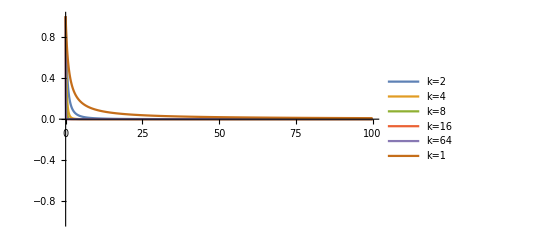

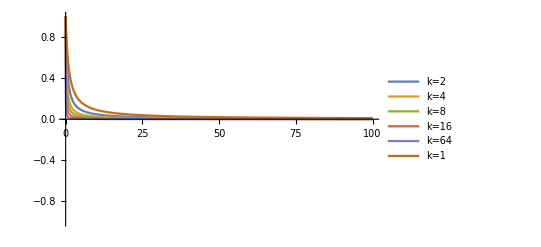

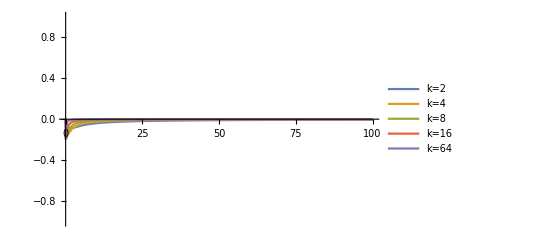

```mathematica
(* Plot convergence as function of dt*xi for k=2,4,8,16,64, with same RK scheme on both levels *)
p = 1;
ver = -1;
s=1;
butcher = GetButcher["SDIRK",p,"A",s,ver];
A=butcher[[1]];
b=butcher[[2]];
A //MatrixForm
(*Limit[lambdak[x,1,A,b],{x->100000000}]*)
xmax = 100;
Plot[{lambdak[x,2,A,b],lambdak[x,4,A,b],lambdak[x,7,A,b],lambdak[x,16,A,b],lambdak[x,64,A,b],lambdak[x,1,A,b]},{x,0,xmax},AxesStyle->Directive[Black,Thickness[linethick]],TicksStyle->Directive[Black,Thickness[linethick],fontsize],
PlotRange->{{0,xmax},{-1,1}},PlotRangeClipping->True,Frame->False,AspectRatio->1/GoldenRatio, PlotLegends->Placed[{"k=2","k=4","k=8","k=16","k=64","k=1"},Right]]
Plot[{mu[x,2,A,b],mu[x,4,A,b],mu[x,7,A,b],mu[x,16,A,b],mu[x,64,A,b],mu[x,1,A,b]},{x,0,xmax},PlotRange->{{0,xmax},{-1,1}},PlotRangeClipping->True,Frame->False,AspectRatio->1/GoldenRatio, 
AxesStyle->Directive[Black,Thickness[linethick]],TicksStyle->Directive[Black,Thickness[linethick],fontsize],PlotLegends->Placed[{"k=2","k=4","k=8","k=16","k=64","k=1"},Right]]
Plot[{lambdak[x,2,A,b]-mu[x,2,A,b],lambdak[x,4,A,b]-mu[x,4,A,b],lambdak[x,7,A,b]-mu[x,7,A,b],lambdak[x,16,A,b]-mu[x,16,A,b],lambdak[x,64,A,b]-mu[x,64,A,b]},{x,0,xmax},PlotRange->{{0,xmax},{-1,1}},PlotRangeClipping->True,Frame->False,AspectRatio->1/GoldenRatio, PlotLegends->Placed[{"k=2","k=4","k=8","k=16","k=64"},Right]]
```

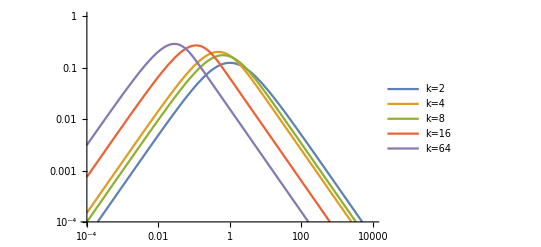

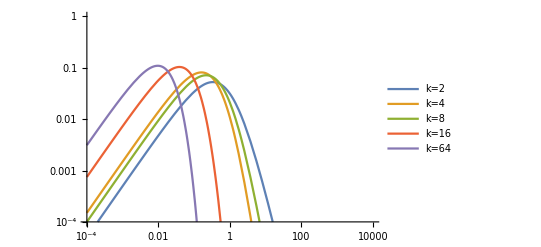

```mathematica
(* Log-log plots and functions to find limits and max *)
xmax = 10000;
w=1;
LogLogPlot[{phiF[x,2,A,b,1],phiF[x,4,A,b,w],phiF[x,3,A,b,w],phiF[x,16,A,b,w],phiF[x,64,A,b,w]},{x,10^(-4),xmax},
PlotRange->{{10^(-4),xmax},{10^(-4),1}},PlotRangeClipping->True,Frame->False,AspectRatio->1/GoldenRatio, AxesStyle->Directive[Black,Thickness[linethick]],TicksStyle->Directive[Black,Thickness[linethick],fontsize],PlotLegends->Placed[{"k=2","k=4","k=8","k=16","k=64"},Right]]
LogLogPlot[{phiFCF[x,2,A,b,w],phiFCF[x,4,A,b,w],phiFCF[x,3,A,b,w],phiFCF[x,16,A,b,w],phiFCF[x,64,A,b,w]},{x,10^(-4),xmax},PlotRange->{{10^(-4),xmax},{10^(-4),1}},PlotRangeClipping->True,Frame->False,AspectRatio->1/GoldenRatio, AxesStyle->Directive[Black,Thickness[linethick]],TicksStyle->Directive[Black,Thickness[linethick],fontsize],PlotLegends->Placed[{"k=2","k=4","k=8","k=16","k=64"},Right]]
(*maxF2=ArgMax[{phiF[x,2,A,b,w],0≤x≤Infinity},x];
maxF4=ArgMax[{phiF[x,4,A,b,w],0≤x≤Infinity},x];
maxF8=ArgMax[{phiF[x,8,A,b,w],0≤x≤Infinity},x];
maxF16=ArgMax[{phiF[x,16,A,b,w],0≤x≤Infinity},x];
maxF32=ArgMax[{phiF[x,32,A,b,w],0≤x≤Infinity},x];
maxF64=ArgMax[{phiF[x,64,A,b,w],0≤x≤Infinity},x];
maxFCF2=ArgMax[{phiFCF[x,2,A,b,w],0≤x≤Infinity},x];
maxFCF4=ArgMax[{phiFCF[x,4,A,b,w],0≤x≤Infinity},x];
maxFCF8=ArgMax[{phiFCF[x,8,A,b,w],0≤x≤Infinity},x];
maxFCF16=ArgMax[{phiFCF[x,16,A,b,w],0≤x≤Infinity},x];
maxFCF32=ArgMax[{phiFCF[x,32,A,b,w],0≤x≤Infinity},x];
maxFCF64=ArgMax[{phiFCF[x,64,A,b,w],0≤x≤Infinity},x];
res = {{maxF2,maxFCF2,maxF4,maxFCF4,maxF8,maxFCF8,maxF16,maxFCF16,maxF32,maxFCF32,maxF64,maxFCF64},{phiF[maxF2,2,A,b,w],phiFCF[maxFCF2,2,A,b,w],phiF[maxF4,4,A,b,w],phiFCF[maxFCF4,4,A,b,w],phiF[maxF8,8,A,b,w],phiFCF[maxFCF8,8,A,b,w],phiF[maxF16,16,A,b,w],phiFCF[maxFCF16,16,A,b,w],phiF[maxF32,32,A,b,w],phiFCF[maxFCF32,32,A,b,w],phiF[maxF64,64,A,b,w],phiFCF[maxFCF64,64,A,b,w]}} //MatrixForm
(*limF2=Limit[phiF[x,2,A,b],{x->Infinity}];
limF4=Limit[phiF[x,4,A,b],{x->Infinity}];
limF8=Limit[phiF[x,8,A,b],{x->Infinity}];
limF16=Limit[phiF[x,16,A,b],{x->Infinity}];
limF32=Limit[phiF[x,32,A,b],{x->Infinity}];
limF64=Limit[phiF[x,64,A,b],{x->Infinity}];
limFCF2=Limit[phiFCF[x,2,A,b],{x->Infinity}];
limFCF4=Limit[phiFCF[x,4,A,b],{x->Infinity}];
limFCF8=Limit[phiFCF[x,8,A,b],{x->Infinity}];
limFCF16=Limit[phiFCF[x,16,A,b],{x->Infinity}];
limFCF32=Limit[phiFCF[x,32,A,b],{x->Infinity}];
limFCF64=Limit[phiFCF[x,64,A,b],{x->Infinity}];*)
limF2=Limit[phiF[x,2,A,b,w],{x->10^10}];
limF4=Limit[phiF[x,4,A,b,w],{x->10^10}];
limF8=Limit[phiF[x,8,A,b,w],{x->10^10}];
limF16=Limit[phiF[x,16,A,b,w],{x->10^10}];
limF32=Limit[phiF[x,32,A,b,w],{x->10^10}];
limF64=Limit[phiF[x,64,A,b,w],{x->10^10}];
limFCF2=Limit[phiFCF[x,2,A,b,w],{x->10^10}];
limFCF4=Limit[phiFCF[x,4,A,b,w],{x->10^10}];
limFCF8=Limit[phiFCF[x,8,A,b,w],{x->10^10}];
limFCF16=Limit[phiFCF[x,16,A,b,w],{x->10^10}];
limFCF32=Limit[phiFCF[x,32,A,b,w],{x->10^10}];
limFCF64=Limit[phiFCF[x,64,A,b,w],{x->10^10}];
lim={{limF2,limFCF2,limF4,limFCF4,limF8,limFCF8,limF16,limFCF16,limF32,limFCF32,limF64,limFCF64}}//MatrixForm
zerF2=x/.FindRoot[phiF[x,2,A,b,w]==1,{x,25}];
zerF4=x/.FindRoot[phiF[x,4,A,b,w]==1,{x,25}];
zerF8=x/.FindRoot[phiF[x,8,A,b,w]==1,{x,25}];
zerF16=x/.FindRoot[phiF[x,16,A,b,w]==1,{x,25}];
zerF32=x/.FindRoot[phiF[x,32,A,b,w]==1,{x,25}];
zerF64=x/.FindRoot[phiF[x,64,A,b,w]==1,{x,25}];
zerFCF2=x/.FindRoot[phiFCF[x,2,A,b,w]==1,{x,25}];
zerFCF4=x/.FindRoot[phiFCF[x,4,A,b,w]==1,{x,25}];
zerFCF8=x/.FindRoot[phiFCF[x,8,A,b,w]==1,{x,25}];
zerFCF16=x/.FindRoot[phiFCF[x,16,A,b,w]==1,{x,25}];
zerFCF32=x/.FindRoot[phiFCF[x,32,A,b,w]==1,{x,25}];
zerFCF64=x/.FindRoot[phiFCF[x,64,A,b,w]==1,{x,25}];
zer={{zerF2,zerFCF2,zerF4,zerFCF4,zerF8,zerFCF8,zerF16,zerFCF16,zerF32,zerFCF32,zerF64,zerFCF64}}//MatrixForm*)
(* Take limit of convergence as dt*xi -> -\infty. *)
(*Limit[phiF[x,20,{x->Infinity}]*)
(*Limit[phiFCF[x,3,A,b],{x->Infinity}]*)
(*phiF[-0.1,5,A,b]*)
```

(0.788675 | 0
-0.57735 | 0.788675)

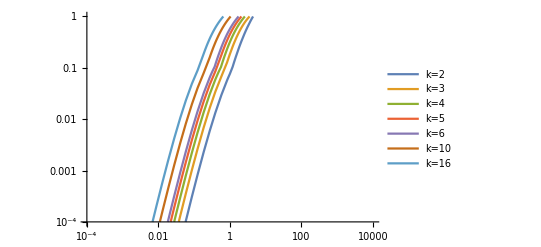

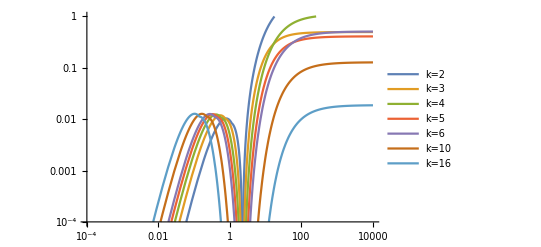

FindMaxValue::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

3.03985

0.012737

0.000155768

```mathematica
(* Plot convergence as function of dt*xi for k=2,4,8,16,64, with *different* RK schemes *)
butcher = GetButcher["ESDIRK",3,"A",3,1];
Af=butcher[[1]];
bf=butcher[[2]];
butcherC = GetButcher["SDIRK",1,"L",2,1];
Ac=butcherC[[1]];
bc=butcherC[[2]];
Ac //MatrixForm
xmax = 10000.0;
w=1;
LogLogPlot[{phiFdiff[x,2,Af,bf,Ac,bc,w],phiFdiff[x,3,Af,bf,Ac,bc,w],phiFdiff[x,4,Af,bf,Ac,bc,w],phiFdiff[x,5,Af,bf,Ac,bc,w],phiFdiff[x,6,Af,bf,Ac,bc,w],phiFdiff[x,10,Af,bf,Ac,bc,w],phiFdiff[x,16,Af,bf,Ac,bc,w]},{x,0.0001,xmax},
PlotRange->{{0.0001,xmax},{10^(-4),1}},PlotRangeClipping->True,Frame->False,AspectRatio->1/GoldenRatio, AxesStyle->Directive[Black,Thickness[linethick]],TicksStyle->Directive[Black,Thickness[linethick],fontsize],PlotLegends->Placed[{"k=2","k=3","k=4","k=5","k=6","k=10","k=16"},Right]]
LogLogPlot[{phiFCFdiff[x,2,Af,bf,Ac,bc,w],phiFCFdiff[x,3,Af,bf,Ac,bc,w],phiFCFdiff[x,4,Af,bf,Ac,bc,w],phiFCFdiff[x,5,Af,bf,Ac,bc,w],phiFCFdiff[x,6,Af,bf,Ac,bc,w],phiFCFdiff[x,10,Af,bf,Ac,bc,w],phiFCFdiff[x,16,Af,bf,Ac,bc,w]},{x,0.0001,xmax},PlotRange->{{0.0001,xmax},{10^(-4),1}},AxesStyle->Directive[Black,Thickness[linethick]],TicksStyle->Directive[Black,Thickness[linethick],fontsize],PlotRangeClipping->True,Frame->False,AspectRatio->1/GoldenRatio, PlotLegends->Placed[{"k=2","k=3","k=4","k=5","k=6","k=10","k=16"},Right]]

(* Take limit of convergence as dt*xi -> -\infty. *)
FindMaxValue[phiFdiff[x,8,Af,bf,Ac,bc,w],{x,0.1}]
FindMaxValue[phiFCFdiff[x,16,Af,bf,Ac,bc,w],{x,0.1}]
phiFCFdiff[5,8,Af,bf,Ac,bc,w]
```

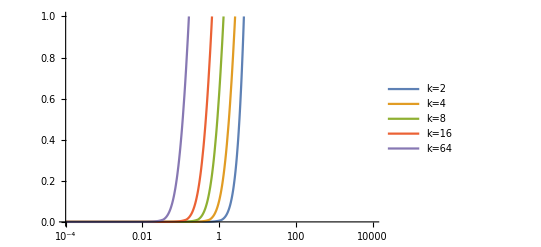

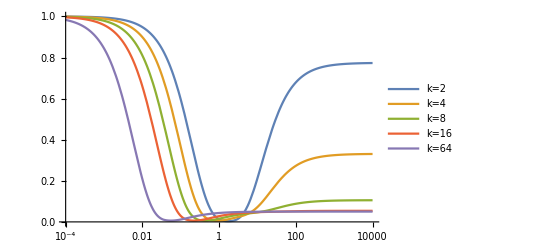

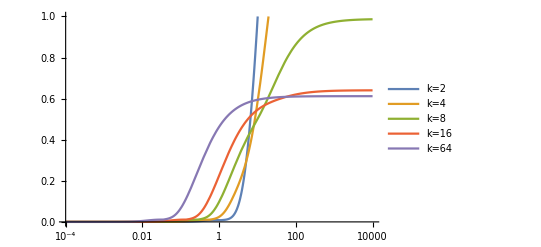

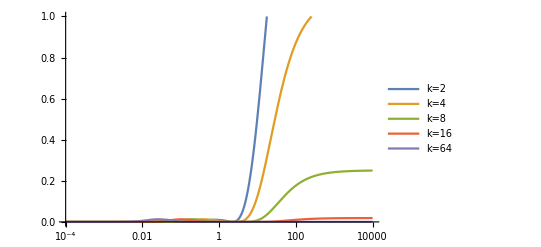

```mathematica
(* Test damping as in theta-parareal paper, by applying theta directly to \Psi *)
p = 3;
ver = -1;
s=3;
butcher = GetButcher["ESDIRK",p,"A",s,ver];
A=butcher[[1]];
b=butcher[[2]];
xmax = 10000;
w1=1;
w2=0.25;
LogLinearPlot[{phiF[x,2,A,b,w1]^2,phiF[x,4,A,b,w1]^2,phiF[x,8,A,b,w1]^2,phiF[x,16,A,b,w1]^2,phiF[x,64,A,b,w1]^2},{x,10^(-4),xmax},
PlotRange->{{10^(-4),xmax},{0,1}},PlotRangeClipping->True,Frame->False,AspectRatio->1/GoldenRatio, AxesStyle->Directive[Black,Thickness[linethick]],TicksStyle->Directive[Black,Thickness[linethick],fontsize],PlotLegends->Placed[{"k=2","k=4","k=8","k=16","k=64"},Right]]
LogLinearPlot[{phiF[x,2,A,b,w2]^2,phiF[x,4,A,b,w2]^2,phiF[x,8,A,b,w2]^2,phiF[x,16,A,b,w2]^2,phiF[x,64,A,b,w2]^2},{x,10^(-4),xmax},
PlotRange->{{10^(-4),xmax},{0,1}},PlotRangeClipping->True,Frame->False,AspectRatio->1/GoldenRatio, AxesStyle->Directive[Black,Thickness[linethick]],TicksStyle->Directive[Black,Thickness[linethick],fontsize],PlotLegends->Placed[{"k=2","k=4","k=8","k=16","k=64"},Right]]
LogLinearPlot[{phiF2[x,2,A,b,w1,w2],phiF2[x,4,A,b,w1,w2],phiF2[x,8,A,b,w1,w2],phiF2[x,16,A,b,w1,w2],phiF2[x,64,A,b,w1,w2]},{x,10^(-4),xmax},
PlotRange->{{10^(-4),xmax},{0,1}},PlotRangeClipping->True,Frame->False,AspectRatio->1/GoldenRatio, AxesStyle->Directive[Black,Thickness[linethick]],TicksStyle->Directive[Black,Thickness[linethick],fontsize],PlotLegends->Placed[{"k=2","k=4","k=8","k=16","k=64"},Right]]
LogLinearPlot[{phiFCF[x,2,A,b,w1],phiFCF[x,4,A,b,w1],phiFCF[x,8,A,b,w1],phiFCF[x,16,A,b,w1],phiFCF[x,64,A,b,w1]},{x,10^(-4),xmax},
PlotRange->{{10^(-4),xmax},{0,1}},PlotRangeClipping->True,Frame->False,AspectRatio->1/GoldenRatio, AxesStyle->Directive[Black,Thickness[linethick]],TicksStyle->Directive[Black,Thickness[linethick],fontsize],PlotLegends->Placed[{"k=2","k=4","k=8","k=16","k=64"},Right]]
(*Roots[lambdak[x,k,A,b]-mu[x,k,A,b]==0,x]*)
```

(0 | 0 | 0 | 0
0.5 | 0 | 0 | 0
0. | 0.5 | 0 | 0
0. | 0. | 1. | 0)

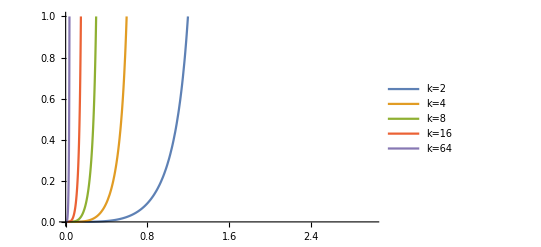

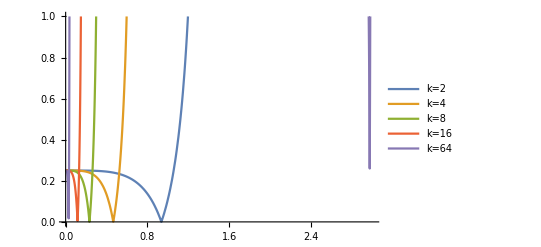

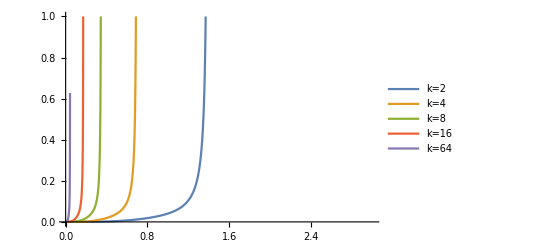

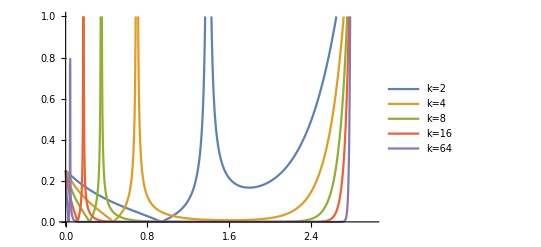

```mathematica
(* Test traditional damping by applying weight omega to coarse-grid correction operator *)
p = 4;
ver = -1;
s=3;
butcher = GetButcher["ERK",p,"A",s,ver];
A=butcher[[1]];
b=butcher[[2]];
A //MatrixForm
xmax = 3;
w1=1.25;
Plot[{phiF[x,2,A,b,1],phiF[x,4,A,b,1],phiF[x,8,A,b,1],phiF[x,16,A,b,1],phiF[x,64,A,b,1]},{x,10^(-10),xmax},
PlotRange->{{10^(-10),xmax},{0,1}},PlotRangeClipping->True,Frame->False,AspectRatio->1/GoldenRatio, AxesStyle->Directive[Black,Thickness[linethick]],TicksStyle->Directive[Black,Thickness[linethick],fontsize],PlotLegends->Placed[{"k=2","k=4","k=8","k=16","k=64"},Right]]
Plot[{phiFdamp[x,2,A,b,w1],phiFdamp[x,4,A,b,w1],phiFdamp[x,8,A,b,w1],phiFdamp[x,16,A,b,w1],phiFdamp[x,64,A,b,w1]},{x,10^(-10),xmax},
PlotRange->{{10^(-10),xmax},{0,1}},PlotRangeClipping->True,Frame->False,AspectRatio->1/GoldenRatio, AxesStyle->Directive[Black,Thickness[linethick]],TicksStyle->Directive[Black,Thickness[linethick],fontsize],PlotLegends->Placed[{"k=2","k=4","k=8","k=16","k=64"},Right]]
Plot[{phiFCF[x,2,A,b,1],phiFCF[x,4,A,b,1],phiFCF[x,8,A,b,1],phiFCF[x,16,A,b,1],phiFCF[x,64,A,b,1]},{x,10^(-10),xmax},
PlotRange->{{10^(-10),xmax},{0,1}},PlotRangeClipping->True,Frame->False,AspectRatio->1/GoldenRatio, AxesStyle->Directive[Black,Thickness[linethick]],TicksStyle->Directive[Black,Thickness[linethick],fontsize],PlotLegends->Placed[{"k=2","k=4","k=8","k=16","k=64"},Right]]
Plot[{phiFCFdamp[x,2,A,b,w1],phiFCFdamp[x,4,A,b,w1],phiFCFdamp[x,8,A,b,w1],phiFCFdamp[x,16,A,b,w1],phiFCFdamp[x,64,A,b,w1]},{x,10^(-10),xmax},
PlotRange->{{10^(-10),xmax},{0,1}},PlotRangeClipping->True,Frame->False,AspectRatio->1/GoldenRatio, AxesStyle->Directive[Black,Thickness[linethick]],TicksStyle->Directive[Black,Thickness[linethick],fontsize],PlotLegends->Placed[{"k=2","k=4","k=8","k=16","k=64"},Right]]
```

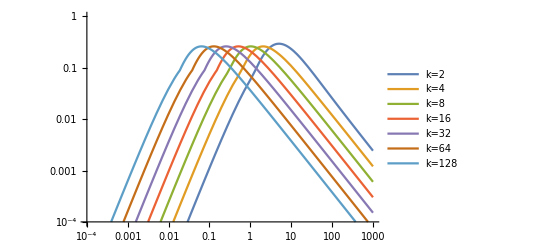

{0.337817,{x→0.0747424,k→114.834,a→0.8}}

{0.261547,{x→0.0685318,k→119.222}}

{0.294623,{x→5.01522}}

```mathematica
(* Compute TR/BDF2 alegbraically *)
G[a_,z_]:= (2*a-4+z*(a^2-2*a+2))/(z^2*a*(a-1) - z*(2-a^2)+2*a-4);
Gp[k_,a_,z_]:=Abs[G[a,z]^k - G[a,k*z]]/(1 - Abs[G[a,k*z]]);
alpha= 2-Sqrt[2];
amin=0.043;
amax=0.8;
LogLogPlot[{Gp[2,alpha,x],Gp[4,alpha,x],Gp[8,alpha,x],Gp[16,alpha,x],Gp[32,alpha,x],Gp[64,alpha,x],Gp[128,alpha,x]},{x,0.0001,xmax},
PlotRange->{{0.0001,xmax},{10^(-4),1}},PlotRangeClipping->True,Frame->False,AspectRatio->1/GoldenRatio, AxesStyle->Directive[Black,Thickness[linethick]],TicksStyle->Directive[Black,Thickness[linethick],fontsize],PlotLegends->Placed[{"k=2","k=4","k=8","k=16","k=32","k=64","k=128"},Right]]
maxF1=FindMaximum[{Gp[k,a,x],0≤x≤Infinity && k≥2 && amin<=a<=amax},{x,k,a} ]
maxF2=FindMaximum[{Gp[k,alpha,x],0≤x≤Infinity && k≥2 },{x,k} ]
maxF3=FindMaximum[{Gp[2,alpha,x],0≤x≤Infinity },{x} ]
```

```mathematica
(* Plot eigenvalues \lambda for different schemes *)
```

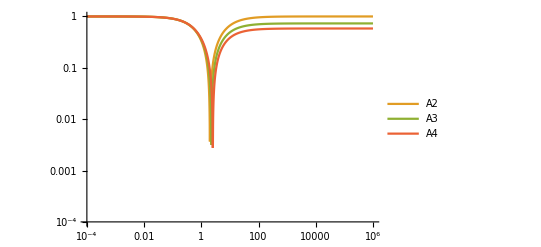

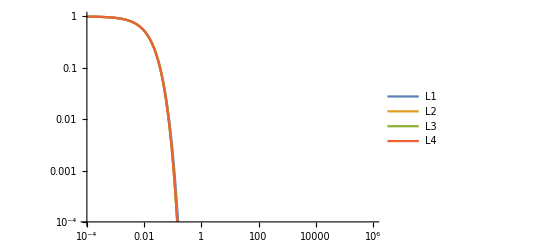

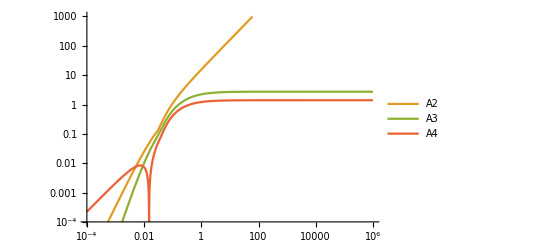

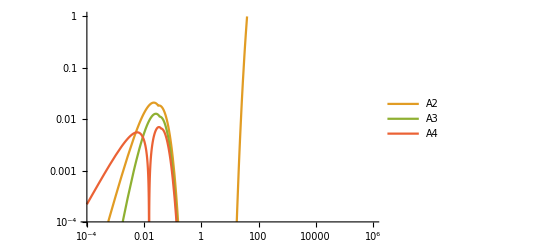

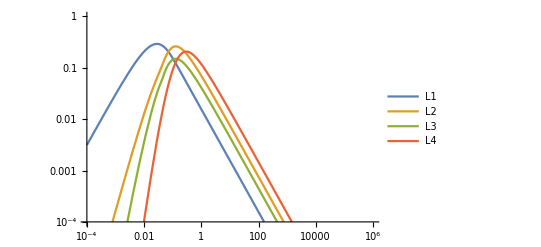

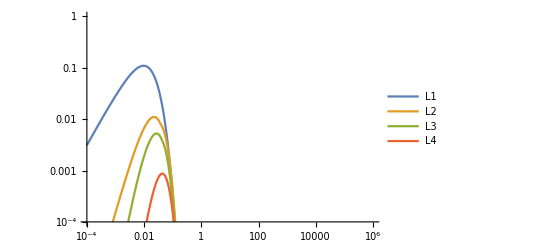

```mathematica
butcher = GetButcher["SDIRK",1,"A",1,1];
A1=butcher[[1]];
ba1=butcher[[2]];
butcher = GetButcher["SDIRK",2,"A",1,1];
A2=butcher[[1]];
ba2=butcher[[2]];
butcher = GetButcher["SDIRK",3,"A",2,1];
A3=butcher[[1]];
ba3=butcher[[2]];
butcher = GetButcher["SDIRK",4,"A",3,1];
A4=butcher[[1]];
ba4=butcher[[2]];
butcher = GetButcher["SDIRK",1,"L",1,1];
L1=butcher[[1]];
bl1=butcher[[2]];
butcher = GetButcher["SDIRK",2,"L",2,1];
L2=butcher[[1]];
bl2=butcher[[2]];
butcher = GetButcher["SDIRK",3,"L",3,1];
L3=butcher[[1]];
bl3=butcher[[2]];
butcher = GetButcher["SDIRK",4,"L",5,1];
L4=butcher[[1]];
bl4=butcher[[2]];
k=64;
xmax = 10^6;
LogLogPlot[{0*x,Abs[lambdak[x,1,A2,ba2]],Abs[lambdak[x,1,A3,ba3]],Abs[lambdak[x,1,A4,ba4]]},{x,10^(-4),xmax},
PlotRange->{{10^(-4),xmax},{10^(-4),1}},PlotRangeClipping->True,Frame->False,AspectRatio->1/GoldenRatio, AxesStyle->Directive[Black,Thickness[linethick]],TicksStyle->Directive[Black,Thickness[linethick],fontsize],PlotLegends->Placed[{"","A2","A3","A4"},Right]]
LogLogPlot[{Abs[lambdak[x,1,L1,bl1]],Abs[lambdak[x,1,L2,bl2]],Abs[lambdak[x,1,L3,bl3]],Abs[lambdak[x,1,L4,bl4]]},{x,10^(-4),xmax},
PlotRange->{{10^(-4),xmax},{10^(-4),1}},PlotRangeClipping->True,Frame->False,AspectRatio->1/GoldenRatio, AxesStyle->Directive[Black,Thickness[linethick]],TicksStyle->Directive[Black,Thickness[linethick],fontsize],PlotLegends->Placed[{"L1","L2","L3","L4"},Right]]
LogLogPlot[{Abs[lambdak[x,k,A2,ba2]],Abs[lambdak[x,k,A3,ba3]],Abs[lambdak[x,k,A4,ba4]]},{x,10^(-4),xmax},
PlotRange->{{10^(-4),xmax},{10^(-4),1}},PlotRangeClipping->True,Frame->False,AspectRatio->1/GoldenRatio, AxesStyle->Directive[Black,Thickness[linethick]],TicksStyle->Directive[Black,Thickness[linethick],fontsize],PlotLegends->Placed[{"A2","A3","A4"},Right]]
LogLogPlot[{Abs[lambdak[x,k,L1,bl1]],Abs[lambdak[x,k,L2,bl2]],Abs[lambdak[x,k,L3,bl3]],Abs[lambdak[x,k,L4,bl4]]},{x,10^(-4),xmax},
PlotRange->{{10^(-4),xmax},{10^(-4),1}},PlotRangeClipping->True,Frame->False,AspectRatio->1/GoldenRatio, AxesStyle->Directive[Black,Thickness[linethick]],TicksStyle->Directive[Black,Thickness[linethick],fontsize],PlotLegends->Placed[{"L1","L2","L3","L4"},Right]]
LogLogPlot[{0*x,phiF[x,k,A2,ba2,1],phiF[x,k,A3,ba3,1],phiF[x,k,A4,ba4,1]},{x,10^(-4),xmax},
PlotRange->{{10^(-4),xmax},{10^(-4),1000}},PlotRangeClipping->True,Frame->False,AspectRatio->1/GoldenRatio, AxesStyle->Directive[Black,Thickness[linethick]],TicksStyle->Directive[Black,Thickness[linethick],fontsize],PlotLegends->Placed[{"","A2","A3","A4"},Right]]
LogLogPlot[{0*x,phiFCF[x,k,A2,ba2,1],phiFCF[x,k,A3,ba3,1],phiFCF[x,k,A4,ba4,1]},{x,10^(-4),xmax},
PlotRange->{{10^(-4),xmax},{10^(-4),1}},PlotRangeClipping->True,Frame->False,AspectRatio->1/GoldenRatio, AxesStyle->Directive[Black,Thickness[linethick]],TicksStyle->Directive[Black,Thickness[linethick],fontsize],PlotLegends->Placed[{"","A2","A3","A4"},Right]]
LogLogPlot[{phiF[x,k,L1,bl1,1],phiF[x,k,L2,bl2,1],phiF[x,k,L3,bl3,1],phiF[x,k,L4,bl4,1]},{x,10^(-4),xmax},
PlotRange->{{10^(-4),xmax},{10^(-4),1}},PlotRangeClipping->True,Frame->False,AspectRatio->1/GoldenRatio, AxesStyle->Directive[Black,Thickness[linethick]],TicksStyle->Directive[Black,Thickness[linethick],fontsize],PlotLegends->Placed[{"L1","L2","L3","L4"},Right]]
LogLogPlot[{phiFCF[x,k,L1,bl1,1],phiFCF[x,k,L2,bl2,1],phiFCF[x,k,L3,bl3,1],phiFCF[x,k,L4,bl4,1]},{x,10^(-4),xmax},
PlotRange->{{10^(-4),xmax},{10^(-4),1}},PlotRangeClipping->True,Frame->False,AspectRatio->1/GoldenRatio, AxesStyle->Directive[Black,Thickness[linethick]],TicksStyle->Directive[Black,Thickness[linethick],fontsize],PlotLegends->Placed[{"L1","L2","L3","L4"},Right]]
```